```mathematica
data1:={{0.008,0.004,0.01,0.001},{0.04,0.004,0.112,0.001},{0.08,0.004,0.221,0.001},{0.132,0.004,0.364,0.001},{0.184,0.004,0.516,0.001},{0.256,0.004,0.696,0.001},{0.348,0.004,0.932,0.001},{0.496,0.004,1.251,0.001},{0.728,0.004,1.709,0.001}}
```

```mathematica
data2:={{0.1,0.02,0.01,0.001},{0.2,0.02,0.172,0.001},{0.34,0.02,0.448,0.001},{0.4,0.02,0.449,0.001},{0.6,0.02,0.685,0.001}}
```

```mathematica
Needs["ErrorBarPlots`"]
```

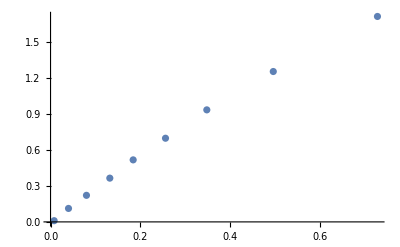

```mathematica
ErrorListPlot[{{#1,#3},ErrorBarPlots`ErrorBar@@{#2,#4}}&@@@data1,PlotRangePadding->{Scaled[0.15],Automatic}]
```

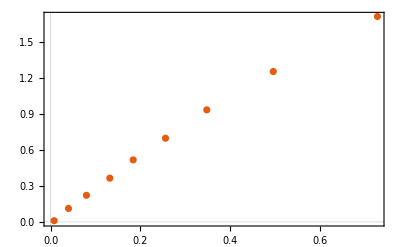

```mathematica
ErrorListPlot[Apply[{{#1,#3},ErrorBar@@{#2,#4}}&,data1,{1}],PlotTheme->"Scientific",PlotRangePadding->{Scaled[0.15],Automatic}]
```

```mathematica
data1fit=LinearModelFit[{#1,#3}&@@@data1,x,x]
```

FittedModel[0.0458772+2.37593 x]

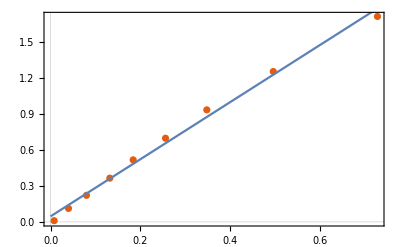

```mathematica
Show[ErrorListPlot[{{#1,#3},ErrorBarPlots`ErrorBar@@{#2,#4}}&@@@data1,PlotRangePadding->{Scaled[0.15],Automatic},PlotTheme->"Scientific"],Plot[data1fit[x],{x,0,1}]]
```

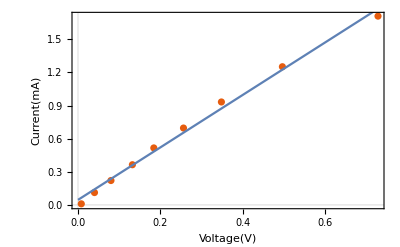

```mathematica
Show[%16,FrameLabel->{{HoldForm[Current[mA]],None},{HoldForm[Voltage[V]],None}},PlotLabel->None,LabelStyle->{FontFamily->"Garamond Premier Pro",12,GrayLevel[0]}]
```

```mathematica
data2fit=LinearModelFit[{#1,#3}&@@@data2,x,x]
```

FittedModel[-0.0907996+1.35244 x]

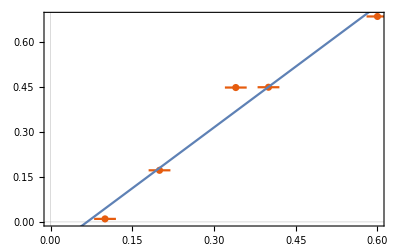

```mathematica
Show[ErrorListPlot[{{#1,#3},ErrorBarPlots`ErrorBar@@{#2,#4}}&@@@data2,PlotRangePadding->{Scaled[0.15],Automatic},PlotTheme->"Scientific"],Plot[data2fit[x],{x,0,1}]]
```

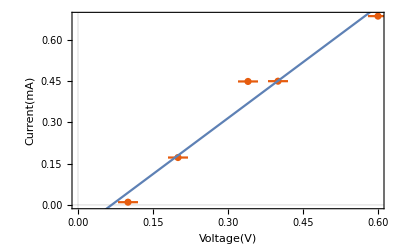

```mathematica
Show[%23,FrameLabel->{{HoldForm[Current[mA]],None},{HoldForm[Voltage[V]],None}},PlotLabel->None,LabelStyle->{FontFamily->"Garamond Premier Pro",12,GrayLevel[0]}]
```